Here we define the boat and the water using ImplicitRegion, and the underwater section as the intersection of the boat and the water using RegionIntersection - we don’t have to use this function - we could write our own definition of the underwater section, but if you look at the expression you will notice that it is exactly what you would have defined anyway. We are using a parabola for the boat, and a variable d for the water. Since Manipulate can’t “see” d inside of water and under, we have to replace d with a local variable, which we call dd, so that Manipulate can do its work. We’ve set the name of the variable dd to be draft, and we’ve assigned an initial value of 1 with a range from 0 to 2.

```mathematica
boat = ImplicitRegion[x^2/2<y<2&&-2<x<2&&0<y<2,{x,y}]
water = ImplicitRegion[0<y<d&&-2<x<2&&0<y<2,{x,y}]
under = RegionIntersection[boat,water]
Manipulate[RegionPlot[{water/.{d->dd},boat,under/.{d->dd}},AspectRatio->Automatic],{{dd,1,"draft"},0,2,Appearance->"Labeled"}]
```

ImplicitRegion[x^2/2<y<2&&-2<x<2&&0<y<2,{x,y}]

ImplicitRegion[0<y<d&&-2<x<2&&0<y<2,{x,y}]

ImplicitRegion[-2<x<2&&0<y<2&&0<y<d&&x^2/2<y<2,{x,y}]

Here we will compute the mass of the boat and the mass of the displaced water in the underwater section as we vary the position of the water from 0 to 2 - we pass this into the Integrate function as an assumption - it just cleans up the answer. Notice that the answer is a function of d and the form of it should make sense. The underwater section is bounded by a rectangle with height d and width √dso that its area is d^(3/2), and we plot this displacement as a function of d. We then solve for the waterline by finding the value of d where the mass of displaced water is equal to the mass of the boat. We ask for a real solution, and notice we get a list of lists as a result. At this point we don’t want a list of lists - we simply want a number. So we replace the first entry in waterline, using the [[1]] notation, into the variable d, and we convert that to a number and assign it to draft. This last part is likely to be very very confusing.

21000

40000/3 √2 d^(3/2)

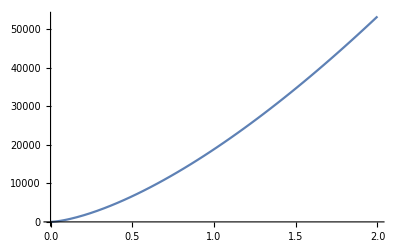

160000/3

{{d→3/4 (7/5)^(2/3) (3/2)^(1/3)}}

1.07443

```mathematica
mass = 10*Integrate[300,{x,y}∈boat]+5000
disp = 10*Integrate[1000,{x,y}∈under,Assumptions->{0<d<2}]
Plot[disp,{d,0,2}]
maxdisp = disp/.{d->2}
waterline = Solve[disp==mass,d,Reals]
draft = N[d/.waterline[[1]]]
```

Now we turn our attention to the center of buoyancy of the submerged region. Rather than just computing it with the correct draft, we first compute it for any depth of water and find that the COB is a really simple expression in terms of d. Notice that the x-position of the COB is zero as expected, and the y-position of the COB is proportional to d. If you think about it, this makes a lot of sense - why? If we replaced the parabola with a rectangle what would we find? We then replace the draft into the COB so that we have the actual placement when the boat is in static equilibrium.

```mathematica
cob = 10*Integrate[1000*{x,y},{x,y}∈under,Assumptions->{0<d<2}]/disp
cob/.{d->draft}
```

{0,(3 d)/5}

{0,0.644656}

Although we could note use a Manipulate and show the COB for any water depth, we will end this section by simply showing the situation in static equilibrium. Any expression that contains d should have d replaced by the actual draft.

```mathematica
Show[RegionPlot[{water/.{d->draft},boat,under/.{d->draft}},AspectRatio->Automatic],ListPlot[{cob/.{d->draft}}]]
```

-Graphics-